```mathematica
Clear["Global*`"]
```

## Developing a Pipeline

Loading the segments comprising one full flight and concatenating

```mathematica
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_1.csv"];
header=data⟦1,;;⟧;data1=data⟦2;;,;;⟧;
data2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_2.csv",HeaderLines->1];
data3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_3.csv",HeaderLines->1];
data4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_4.csv",HeaderLines->1];
data=Join[data1,data2,data3,data4,1];
```

Plotting this data and animating the quad rotors position in the trajectory through time

```mathematica
Module[{pos,downSample},
pos=data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Animate[
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed"]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{pos⟦n⟧},PlotStyle->{Red,Large}]
],
{n,1,Length[pos],1},
AnimationRate->2000
]
]
```

```mathematica
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_2.csv"];
header=data⟦1,;;⟧;data=data⟦2;;,;;⟧;
```

```mathematica
Module[{pos,downSample},
pos=data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Animate[
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed"]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{pos⟦n⟧},PlotStyle->{Red,Large}]
],
{n,1,Length[pos],1}
]
]
```

We want to model the the force from each motor/rotor i, F_i.

(v^·)_B=1/m F_B-ω_B×v_B-Qᵀg
F_B=∑_(i∈{Motors}) F_i
F_B=m((v^·)_B+ω_B×v_B+Qᵀg)

The first method we use to do this is the modeling each each

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
F_B=Ω_i

Extract linear acceleration terms

```mathematica
v̇=data⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=data⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=data⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis and gravity terms

```mathematica
g=({{0, 0, -9.81}})ᵀ;
ŷ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}](*+Map[Flatten[#1ᵀ.g]&,ℛ]*);
```

### Evaluating

Now ŷ,

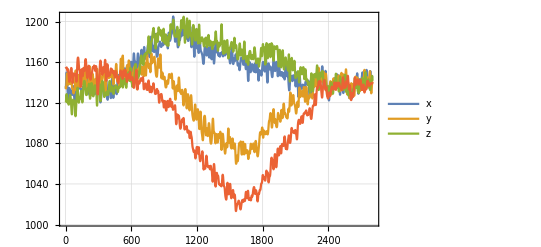

```mathematica
ListPlot[Ωᵀ,PlotTheme->"Detailed",Joined->True,PlotLegends->{"x","y","z"}]
```

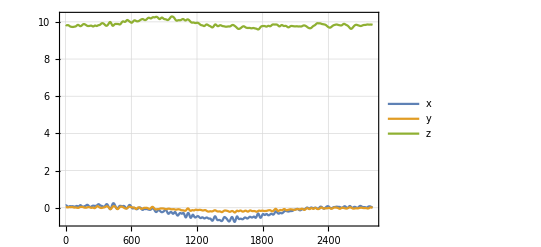

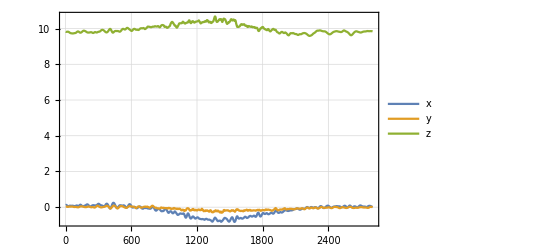

```mathematica
ListPlot[v̇ ᵀ,PlotTheme->"Detailed",Joined->True,PlotLegends->{"x","y","z"}]
ListPlot[ŷ ᵀ,PlotTheme->"Detailed",Joined->True,PlotLegends->{"x","y","z"}]
```

## Training Data

Loading in the training data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_2.csv"];
header=data⟦1,;;⟧;
data=data⟦2;;,;;⟧;
ListPointPlot3D[data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧,PlotTheme->"Detailed"]
```

-Graphics3D-

We want to model the the force from each motor/rotor i, F_i.

(v^·)_B=1/m F_B-ω_B×v_B-Qᵀg
F_B=∑_(i∈{Motors}) F_i

The first method we use to do this is the modeling each each

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
F_B=Ω_i

Extract linear acceleration terms

```mathematica
v̇=data⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=data⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=data⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis and gravity terms

```mathematica
g=({{0, 0, -9.81}})ᵀ;
ŷ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}]+Map[Flatten[#1ᵀ.g]&,ℛ];
x̂=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
```

### Fitting

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
```

```mathematica
𝕂=PseudoInverse[MapThread[𝒻,x̂ ᵀ]].ŷ;
```

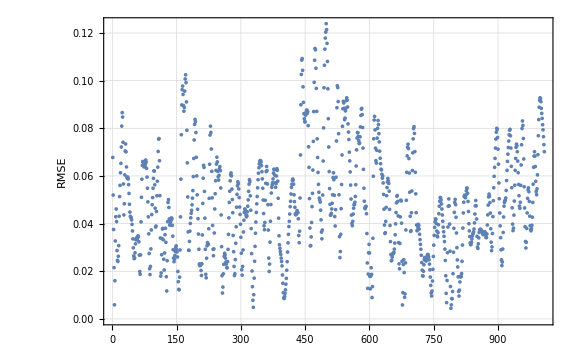

```mathematica
ListPlot[RootMeanSquare/@(MapThread[𝒻,x̂ ᵀ].𝕂-ŷ),PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{None,"RMSE"}]
```

## Testing Data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_4.csv",HeaderLines->1];
(*header=data⟦1,;;⟧;
data=data⟦2;;,;;⟧;*)
ListPointPlot3D[data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧,PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
v̇=data⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=data⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=data⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis and gravity terms

```mathematica
g=({{0, 0, -9.81}})ᵀ;
ȳ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}]-Map[Flatten[#1ᵀ.g]&,ℛ];
(*x̂=Join[Subscript[v, B],Subscript[ω, B],Ω,2];*)
x̄=Join[Subscript[v, B],Ω,2];
```

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̄]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
```

```mathematica
𝕂1=PseudoInverse[MapThread[𝒻,x̄ ᵀ]].ȳ;
```

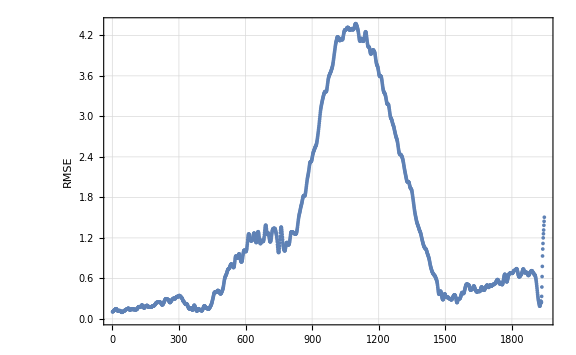

```mathematica
ListPlot[RootMeanSquare/@(MapThread[𝒻,x̄ ᵀ].𝕂-ȳ),PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{None,"RMSE"}]
```

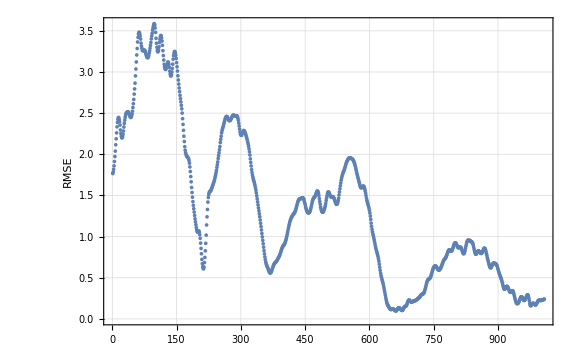

```mathematica
ListPlot[RootMeanSquare/@(MapThread[𝒻,x̂ ᵀ].𝕂1-ŷ),PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{None,"RMSE"}]
```